# The Use of Convolutional Neural Network in Relating Precipitation to Circulation

## From Hourly to Monthly Scale

Baoxiang Pan
2017.7.13

## Abstract

## Introduction

Precipitation prediction in dynamical weather and climate models depends on 1) the predictability of pressure or geopotential height for the forecasting period\cite[] and 2) the successive work of interpreting the pressure field in terms of precipitation events\cite[].  This strategy dates back to the early 20th century when barometric observations were interpolated in space and extrapolated along time, based on which semi-quantitative weather predictions were drawn\cite[]. Since then, the first task has been transforming from empirical inferences to accurate science due to the elucidation of physical laws, increasing computing power and densifying observation networks\cite[]. Such change poses both opportunities and challenges on the subsidiary work of connecting precipitation events to circulation. 
Detailed parameterization schemes involving precipitation processes were developed to close the governing equations for iterative numerical simulation. For unresolved sub-grid scale, precipitation is  represented as a byproduct of moist convection through convective parameterization\cite[]. For grid scale, it is explicitly represented by microphysical parameterization\cite[]. Recent advances in supercomputer is boosting finer resolution that enables bypassing convective parameterization to resolve cloud. 
Despite their scientific illumination and pragmatic importance,  the detailed computing inevitably blurs the cause-and-effect relationship hidden in meteorological phenomena. 

The atmospheric process character greatly depends upon geographical
latitude defining radiation conditions, type and state of the underlying
surface, the region orographic features, etc.

Every of these approaches has both advantages
and disadvantages and, correspondingly, its field of application

Despite the detailling trend., the detail blur the cause-and -effect relationship in synoptic analysis. (we can not hack into numerical models unless doing “whatif” experiments, which involves too much variabilities and computing burdens)
  For instance, distance, intensity, orographic
Statistical methods in understanding , diagnosis correlation field. and PCA. 
a gap fro integrating synoptic and dynamic meteorology\cite[].
Synoptic: 

Dynamical precipitation modelling is usually achieved through the cooperation of convective and microphysical parameterization schemes



illustrating cause-and-effect relationship

Parameterization. Specific to precipitation
storm track

The past decade has seen explosive advance is machine learning, especially deep learning. Why? list the several reasons. See with the help of algorithms. It equipped human with deep insight when observing. 人体机能增强

pre-fixed features to trainable features. 

we use CNN to illustrate the following questions:

1)
2)
3)

dawn of modern meteorology 


early 20th century (Bjerknes)  and have ?? Empirical Extrapolating geopotential height field along time to numerical prediction. It helped the second task. (Existed works  connect to this target) tell about history of extrapolating during the very initial weather forecast semi-quantitative.

subsidiary work of interpreting the pressure field in terms of weather also demands  a large share of attention and is somewhat complex.

Correlation field.

the second task: 
1) focusing on prediction
  	1.1) parameterization
		microphysics
		cumulative parameter 
  	1.2) cloud resolving models
2) focusing on interpretation
	2.1) Correlation Field
	2.2) PCA Combined PCA
What have been done in interpreting? semi-quantitative
what are their drawbacks?
This study is directed toward one aspect of the subsidiary problem. 
Deep learning quantitative observation.	
1) understanding
2) diagnosis: Typical pressure structure, intensity, distance, evolution 
3) improvement

what are the key difficulties?
 p.d.f. of precipitation> 
 	1. is it raining?
 	2. if rains, how heavy?

## Data

Precipitation (all measured in mm/hr)

#### NCEP_Reanalysis

```mathematica
NCEPprecip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]];
	mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]];	
	Table[Import["prate.sfc.gauss."<>ToString[year]<>".nc",{"Datasets","prate"}][[;;,21;;31,126;;133]]*3600,
		{year,1948,2017}]];
Block[{mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]],
	   mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]]},
	{MinMax[mlat],MinMax[mlon]}]
```

{{31.4281,50.4752},{234.375,247.5}}

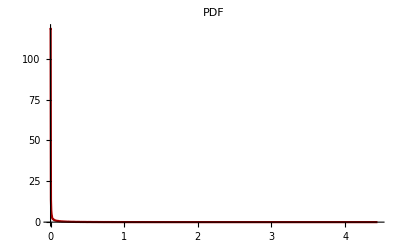
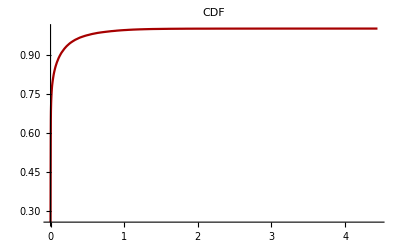

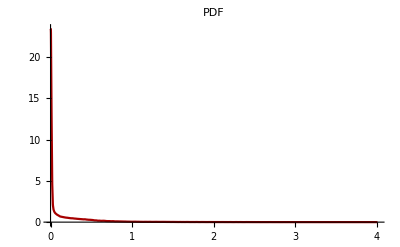
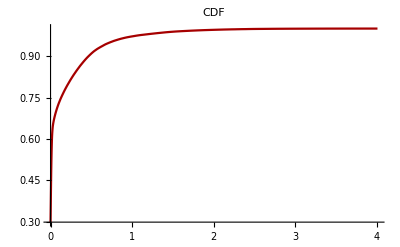

```mathematica
PDFPlot[Flatten[NCEPprecip[[;;,;;,3,8]]]]
PDFPlot[Flatten[NCEPprecip[[;;,;;,3,1]]]]
```

#### ECMWF_Reanalysis

#### CPC_Gauge

```mathematica
CPCprecip=Block[{mlat,mlon,tt,precip1,precip2},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	mlat=Import["precip.V1.0.1948.nc",{"Datasets","lat"}][[48;;]];
	mlon=Import["precip.V1.0.1948.nc",{"Datasets","lon"}][[21;;65]];
	tt=Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	       t},
			t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
			Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t]];
	precip1=Table[Block[{precip},
		precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip],{year,1948,2006}];
	precip1
	(*precip2=Block[{precip},
		precip=Import["precip.V1.0.2007_2017.nc",{"Datasets","rain"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip];
	{precip1,precip2}*)];
```

```mathematica
Dimensions[CPCprecip[[1]]]
Dimensions[CPCprecip]
```

{366,73,45}

{59}

Sea Level Pressure

#### NCEP_Reanalysis

```mathematica
NCEPslp=Block[{mlat,mlon,slat=10,elat=30,slon=85,elon=105},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
	mlat=Import["slp.1948.nc",{"Datasets","lat"}][[slat;;elat]];
	mlon=Import["slp.1948.nc",{"Datasets","lon"}][[slon;;elon]];
	Table[Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}][[;;,slat;;elat,slon;;elon]],
		{year,1948,2017}]];
```

```mathematica
Dimensions[precip[[1]]]
Dimensions[NCEPslp]
```

{1464,11,8}

{70}

#### ECMWF_Reanalysis

## Methodology

```mathematica
winter=Flatten[Table[{Range[1+year*365*4,90*4+year*365*4],
					  Range[270*4+year*365*4,365*4+year*365*4]},{year,0,68}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,51053,100703,100704,100705,100706,100707,100708,100709,100710,100711,100712,100713,100714,100715,100716,100717,100718,100719,100720,100721,100722,100723,100724,100725,100726,100727,100728,100729,100730,100731,100732,100733,100734,100735,100736,100737,100738,100739,100740}
 |  |  |  |

```mathematica
Precip=Block[{m=Mean[Flatten[NCEPprecip,1]]},
	Map[3*Flatten[#-m]&,Flatten[NCEPprecip,1]]][[winter]];
Slp=Block[{m=Mean[Flatten[NCEPslp,1]]},
	Map[{#-m}&,Flatten[NCEPslp,1]]][[winter]];
Dimensions[Precip]
Dimensions[Slp]
{Precip,Slp}=Block[{tempt=RandomSample[Table[{Precip[[i]],Slp[[i]]},{i,Length[Slp]}]]},
	(*tempt=Select[tempt,Mean[#[[1]]]>0.&];*)
	{Map[#[[1]]&,tempt],Map[#[[2]]&,tempt]}];
Dimensions[Precip]
Dimensions[Slp]
```

{51129,88}

{51129,1,21,21}

{51129,88}

{51129,1,21,21}

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 196,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 196,
						 ElementwiseLayer[Ramp],
						 (*DropoutLayer[0.2],*)
						 
						 BatchNormalizationLayer[],
						 88(*,
						 BatchNormalizationLayer[]*)
						 (*ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[]*)
						 },  
					"Input" -> {1,21,21},
					"Output" -> {88}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[Slp]*0.7]
```

35790

```mathematica
ann=NetTrain[CNN,
	Slp[[1;;ptraining]]->Precip[[1;;ptraining]],
	ValidationSet->Table[Slp[[i]]->Precip[[i]],{i,ptraining,Length[Slp]}],
	Method->"ADAM",
	BatchSize->100,
	MaxTrainingRounds -> 2000]
```

NetChain[]

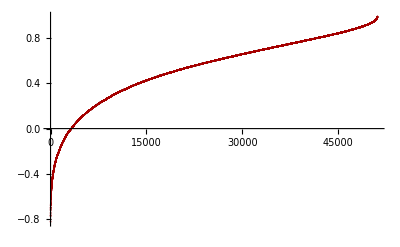

0.534108

```mathematica
test=Table[Correlation[Precip[[day]], ann@Slp[[day]]],{day,Length[Slp]}];
ListPlot[Sort[test]]
Mean[test]
```

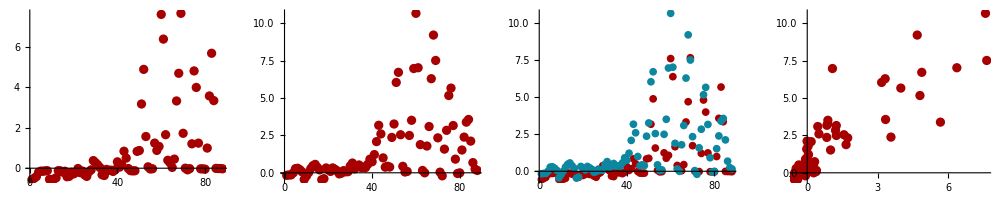
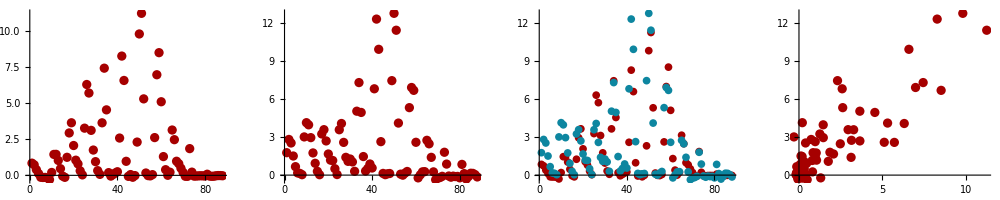
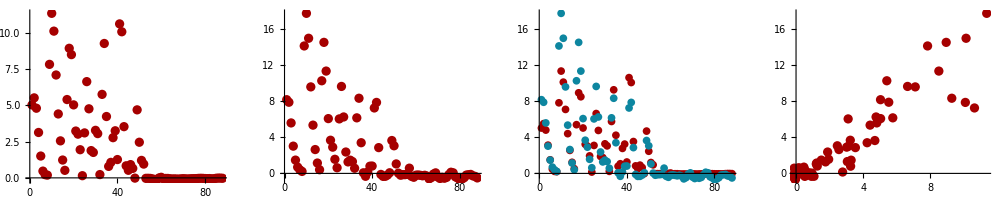
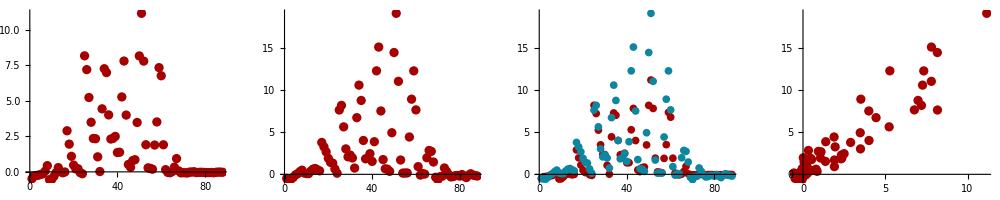
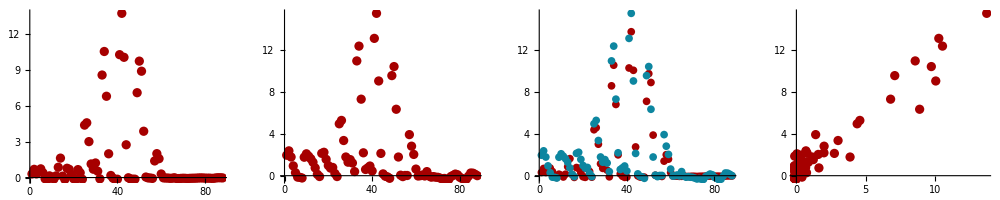
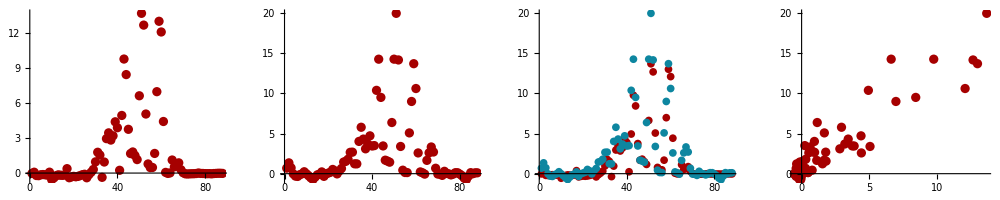
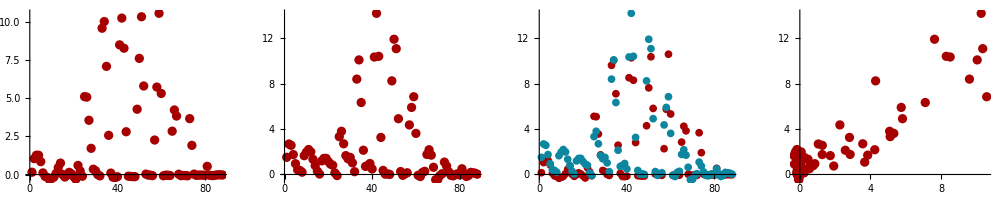
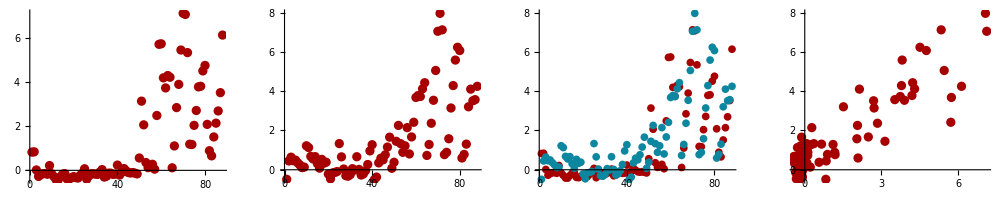

```mathematica
day=Block[{tem=Map[Mean,simu]},
Map[Position[tem,#][[1,1]]&,Sort[tem][[-10;;-1]]]];
Table[
GraphicsRow[{ListPlot[Precip[[day[[i]]]],PlotRange->Full],
			 ListPlot[ann@Slp[[day[[i]]]],PlotRange->Full],
			 ListPlot[{Precip[[day[[i]]]], ann@Slp[[day[[i]]]]},PlotRange->Full],
			 ListPlot[Transpose[{Precip[[day[[i]]]], ann@Slp[[day[[i]]]]}],PlotRange->Full]},
			 ImageSize->1000],{i,Length[day]}]
```

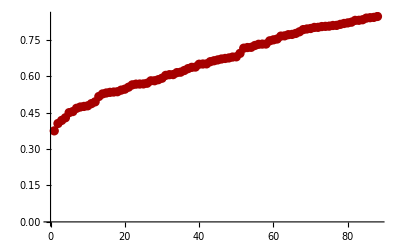

```mathematica
simu=Table[ann@Slp[[day]],{day,Length[Slp]}];
te=Table[Correlation[simu[[;;,i]],Precip[[;;,i]]],{i,88}];
ListPlot[Sort[te]]
```

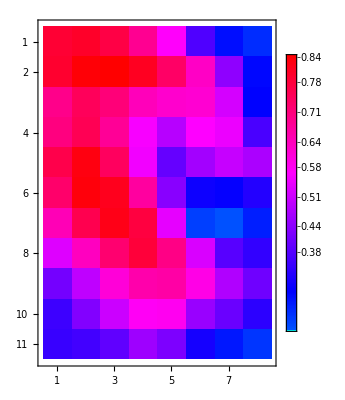

```mathematica
MatrixPlot[ArrayReshape[te,{11,8}],ColorFunction->Hue,
	PlotLegends->Automatic]
```

## Results

## Discussion

## Conclusion

## Operators

```mathematica
PDFPlot[data_]:=Block[{𝒟},
	𝒟 = SmoothKernelDistribution[data];
	Table[Plot[f[𝒟, x], {x, Min[data], Max[data]}, 
	PlotLabel -> f,PlotRange->Full], {f, {PDF, CDF}}]]
```

```mathematica
SetDirectory["/Users/lambda/Documents/S2S/Results"];
Export["ANN.txt",ann]
```

ANN.txt

It's not complicated, it's just a lot of it.

## Network Structure

```mathematica
Precip=Block[{tempt=Map[Select[Flatten[#],NumberQ]&,Flatten[precip,1]],m,v},
	 v=Sqrt[Variance[tempt]];
	 m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[Precip]
```

{21550,1450}

```mathematica
SLP=Block[{tempt=Flatten[slp,1],m,v},
	v=Sqrt[Variance[tempt]];
	m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[SLP]
```

{21550,16,11}

```mathematica
winter=Flatten[Table[{Range[1+year*365,90+year*365],Range[275+year*365,365+year*365]},{year,0,58}]];
```

```mathematica
Precip=Precip[[winter]];
SLP=SLP[[winter]];
```

```mathematica
CNN=NetInitialize[NetChain[{ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2,1],
						 ConvolutionLayer[1, 3], 
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.5],
						 BatchNormalizationLayer[],
						 900,
						 ElementwiseLayer[Ramp],
						 900,
						 ElementwiseLayer[Ramp],
						 1450,
						 BatchNormalizationLayer[]},  
					"Input" -> {1,16,11}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[SLP]*0.7]
```

7475

```mathematica
ann = NetTrain[CNN,
	Map[{#}&,SLP[[1;;ptraining]]] -> Precip[[1;;ptraining]],
	ValidationSet->Table[{SLP[[i]]}->Precip[[i]],{i,ptraining,Length[SLP]}],
	Method->"ADAM",
	BatchSize->200,
	MaxTrainingRounds -> 2000]
```

NetChain[]

```mathematica
Dimensions[SLP]
```

{10679,16,11}

```mathematica
simu=Table[ann@{SLP[[day]]},{day,Length[SLP]}];
```

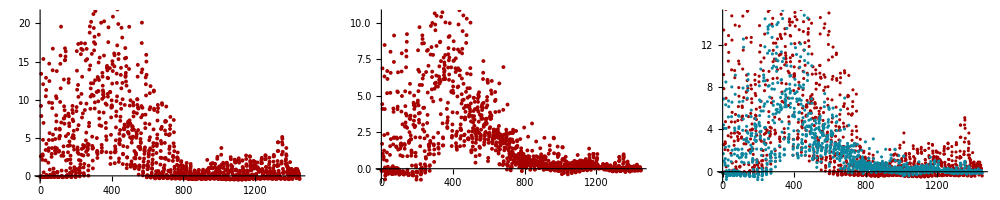

```mathematica
day=3419;
GraphicsRow[{ListPlot[Precip[[day]]],ListPlot[ann@{SLP[[day]]}],ListPlot[{Precip[[day]],ann@{SLP[[day]]}}]},
	ImageSize->1000]
```

```mathematica
test=Table[Correlation[ann@{SLP[[day]]},Precip[[day]]],{day,Length[SLP]}];
```

```mathematica
MinMax[test]
```

{-0.656667,0.973372}

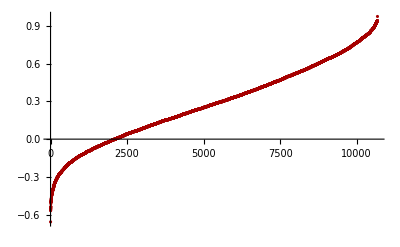

```mathematica
ListPlot[Sort[test]]
```

```mathematica
Position[test,Max[test[[1;;365*10]]]]
```

{{3419}}

### Second level section heading

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.